```mathematica
ClearAll["Global'*"]
(*$PrePrint=If[MatrixQ@#,MatrixForm@#,#]&;*)
(*This code is supposed to find the Transformation stretch tensor for Tetragonal to Monoclinic. This keeps the different lattice correspondences in mind. The Lattice correspondences are listed in the one note
"Effect of stress on transition temperature/LSCO/Tetragonal to monoclinic lattice correspondence". The caluclation od determining the stretch and working out the Claussius Calyperon have been done in "Effect of stress on transition temperature/LSCO/Tetragonal2monoclinic" *)
(*Just run the section corresponding to the correspondence that u are interested in.*)
```

## Section- Lattice correspondence 1a.

```mathematica
(*Defining the refernce {ea_i} and deformed {em_i} basis vectors. *)
(*a0 is the dimensions of the Austenite primitive unit cell.*)
(*a is the dimensions of the Martensite primitive unit cell.*)
ea1[a0_,c0_,a_,b_,c_,β_]:={a0,-a0,0};
ea2[a0_,c0_,a_,b_,c_,β_]:={a0,a0,0};
ea3[a0_,c0_,a_,b_,c_,β_]:={0,0,c0};
em1[a0_,c0_,a_,b_,c_,β_]:={a/Sqrt[2],-a/Sqrt[2],0};
em2[a0_,c0_,a_,b_,c_,β_]:={b/Sqrt[2],b/Sqrt[2],0};
em3[a0_,c0_,a_,b_,c_,β_]:={c*Cos[β]/Sqrt[2],-c*Cos[β]/Sqrt[2],c*Sin[β]};
{ea1[a0,c0,a,b,c,β],ea2[a0,c0,a,b,c,β],ea3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
{em1[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
```

(a0 | a0 | 0
-a0 | a0 | 0
0 | 0 | c0)

(a/(√2) | b/(√2) | (c Cos[β])/(√2)
-a/(√2) | b/(√2) | -(c Cos[β])/(√2)
0 | 0 | c Sin[β])

```mathematica
(*Defining the reference dual and checking that its a dual. This defn works iff the vectors are mutually perpendicular to each other*)
rea1[a0_,c0_,a_,b_,c_,β_]:=1/(ea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β])ea1[a0,c0,a,b,c,β];
rea2[a0_,c0_,a_,b_,c_,β_]:=1/(ea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β])ea2[a0,c0,a,b,c,β];
rea3[a0_,c0_,a_,b_,c_,β_]:=1/(ea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β])ea3[a0,c0,a,b,c,β];
{{rea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea2[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea3[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]}}//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*Checking if the deofmred basis vectors were correctly identified. We know the dot products*)
{em1[a0,c0,a,b,c,β].em1[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β]}//Simplify
```

{a^2,0,a c Cos[β],b^2,0,c^2}

```mathematica
(*USing the stretch tensors form Hanlin.*)
αHan1a[a0_,c0_,a_,b_,c_,β_]:=a/(Sqrt[2]*a0)(*Han is suposed to stand for HAnlin's notation used in the Supplement of the Exploding and weeping paper*)
βHan1a[a0_,c0_,a_,b_,c_,β_]:=b/(Sqrt[2]*a0)
γHan1a[a0_,c0_,a_,b_,c_,β_]:=c/c0
σHan1a[a0_,c0_,a_,b_,c_,β_]:=1/2*(βHan1a[a0,c0,a,b,c,β]+(αHan1a[a0,c0,a,b,c,β]*(αHan1a[a0,c0,a,b,c,β]+γHan1a[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[αHan1a[a0,c0,a,b,c,β]^2+γHan1a[a0,c0,a,b,c,β]^2+2*αHan1a[a0,c0,a,b,c,β]*γHan1a[a0,c0,a,b,c,β]*Sin[β]])
τHan1a[a0_,c0_,a_,b_,c_,β_]:=1/2*(βHan1a[a0,c0,a,b,c,β]-(αHan1a[a0,c0,a,b,c,β]*(αHan1a[a0,c0,a,b,c,β]+γHan1a[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[αHan1a[a0,c0,a,b,c,β]^2+γHan1a[a0,c0,a,b,c,β]^2+2*αHan1a[a0,c0,a,b,c,β]*γHan1a[a0,c0,a,b,c,β]*Sin[β]])
ρHan1a[a0_,c0_,a_,b_,c_,β_]:=(αHan1a[a0,c0,a,b,c,β]*γHan1a[a0,c0,a,b,c,β]*Cos[β])/(Sqrt[2]*Sqrt[αHan1a[a0,c0,a,b,c,β]^2+γHan1a[a0,c0,a,b,c,β]^2+2*αHan1a[a0,c0,a,b,c,β]*γHan1a[a0,c0,a,b,c,β]*Sin[β]])
ηHan1a[a0_,c0_,a_,b_,c_,β_]:=(γHan1a[a0,c0,a,b,c,β]*(γHan1a[a0,c0,a,b,c,β]+αHan1a[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[αHan1a[a0,c0,a,b,c,β]^2+γHan1a[a0,c0,a,b,c,β]^2+2*αHan1a[a0,c0,a,b,c,β]*γHan1a[a0,c0,a,b,c,β]*Sin[β]]
UI[a0_,c0_,a_,b_,c_,β_]:={{σHan1a[a0,c0,a,b,c,β],τHan1a[a0,c0,a,b,c,β],ρHan1a[a0,c0,a,b,c,β]},{τHan1a[a0,c0,a,b,c,β],σHan1a[a0,c0,a,b,c,β],-ρHan1a[a0,c0,a,b,c,β]},{ρHan1a[a0,c0,a,b,c,β],-ρHan1a[a0,c0,a,b,c,β],ηHan1a[a0,c0,a,b,c,β]}};
UII[a0_,c0_,a_,b_,c_,β_]:={{σHan1a[a0,c0,a,b,c,β],τHan1a[a0,c0,a,b,c,β],-ρHan1a[a0,c0,a,b,c,β]},{τHan1a[a0,c0,a,b,c,β],σHan1a[a0,c0,a,b,c,β],ρHan1a[a0,c0,a,b,c,β]},{-ρHan1a[a0,c0,a,b,c,β],ρHan1a[a0,c0,a,b,c,β],ηHan1a[a0,c0,a,b,c,β]}};
UIII[a0_,c0_,a_,b_,c_,β_]:={{σHan1a[a0,c0,a,b,c,β],-τHan1a[a0,c0,a,b,c,β],-ρHan1a[a0,c0,a,b,c,β]},{-τHan1a[a0,c0,a,b,c,β],σHan1a[a0,c0,a,b,c,β],-ρHan1a[a0,c0,a,b,c,β]},{-ρHan1a[a0,c0,a,b,c,β],-ρHan1a[a0,c0,a,b,c,β],ηHan1a[a0,c0,a,b,c,β]}};
UIV[a0_,c0_,a_,b_,c_,β_]:={{σHan1a[a0,c0,a,b,c,β],-τHan1a[a0,c0,a,b,c,β],ρHan1a[a0,c0,a,b,c,β]},{-τHan1a[a0,c0,a,b,c,β],σHan1a[a0,c0,a,b,c,β],ρHan1a[a0,c0,a,b,c,β]},{ρHan1a[a0,c0,a,b,c,β],ρHan1a[a0,c0,a,b,c,β],ηHan1a[a0,c0,a,b,c,β]}};
Manipulate[{"UI=",UI[a0,c0,a,b,c,β]//MatrixForm,"UII=",UII[a0,c0,a,b,c,β]//MatrixForm,"UIII=",UIII[a0,c0,a,b,c,β]//MatrixForm,"UIV=",UIV[a0,c0,a,b,c,β]//MatrixForm},{{a0,1},1,2,0.01},{{c0,1.5},1,2,0.01},{{a,1.1},1,2,0.01},{{b,1.2},1,2,0.01},{{c,1.1},1,2,0.01},{{β,Pi/2+0.1},0,Pi,0.01}]
```

```mathematica
(*Plotting the different variants.*)
(*Anti clockwise is considered positive in here.*)
(*Print["UI=",UI[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["UII=",UII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["UIII=",UIII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["UIV=",UIV[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]*)
em1vII[a0_,c0_,a_,b_,c_,β_]:=UII[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β] (*u1V corresponds to em1 lattice of a Vaiant. We will reuse these.*)
em2vII[a0_,c0_,a_,b_,c_,β_]:=UII[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β] (*u2V corresponds to em2 lattice of a Variant. We will reuse these.*)
em3vII[a0_,c0_,a_,b_,c_,β_]:=UII[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β] (*em3V corresponds to em3 lattice of a Variant. We will reuse these.*)
em1vIII[a0_,c0_,a_,b_,c_,β_]:=UIII[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β] (*em1V corresponds to em1 lattice of a Variant. We will reuse these.*)
em2vIII[a0_,c0_,a_,b_,c_,β_]:=UIII[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β] (*em2V corresponds to em2 lattice of a Variant. We will reuse these.*)
em3vIII[a0_,c0_,a_,b_,c_,β_]:=UIII[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β] (*em3V corresponds to em3 lattice of a Variant. We will reuse these.*)
em1vIV[a0_,c0_,a_,b_,c_,β_]:=UIV[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β] (*em1V corresponds to em1 lattice of a Variant. We will reuse these.*)
em2vIV[a0_,c0_,a_,b_,c_,β_]:=UIV[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β] (*em2V corresponds to em2 lattice of a Variant. We will reuse these.*)
em3vIV[a0_,c0_,a_,b_,c_,β_]:=UIV[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β] (*em3V corresponds to em3 lattice of a Variant. We will reuse these.*)
p={0,0,0};(*Here black to red is em1,black to green is em2,black to blue is em3.*)
Manipulate[{"Variant II ->",Show[Graphics3D[Line[{p,p+em1vII[a0,c0,a,b,c,β],p+em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β],p+em2vII[a0,c0,a,b,c,β],p,p+em3vII[a0,c0,a,b,c,β],p+em3vII[a0,c0,a,b,c,β]+em1vII[a0,c0,a,b,c,β],p+em3vII[a0,c0,a,b,c,β]+em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β],p+em3vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β],p+em3vII[a0,c0,a,b,c,β],p+em3vII[a0,c0,a,b,c,β]+em1vII[a0,c0,a,b,c,β],p+em1vII[a0,c0,a,b,c,β],p+em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β],p+em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β]+em3vII[a0,c0,a,b,c,β],p+em2vII[a0,c0,a,b,c,β]+em3vII[a0,c0,a,b,c,β],p+em2vII[a0,c0,a,b,c,β]}]],Graphics3D[{PointSize[.02],Black,Point[p],Text[Style["O",12],p+0.07*(em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β]+em3vII[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Red,Point[p+em1vII[a0,c0,a,b,c,β]],Text[Style["em_(1, II)",12],p+em1vII[a0,c0,a,b,c,β]+0.07*(em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β]+em3vII[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Green,Point[p+em2vII[a0,c0,a,b,c,β]],Text[Style["em_(2, II)",12],p+em2vII[a0,c0,a,b,c,β]+0.07*(em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β]+em3vII[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Blue,Point[p+em3vII[a0,c0,a,b,c,β]],Text[Style["em_(3, II)",12],p+em3vII[a0,c0,a,b,c,β]+0.07*(em1vII[a0,c0,a,b,c,β]+em2vII[a0,c0,a,b,c,β]+em3vII[a0,c0,a,b,c,β])]}],ImageSize->Large],"Variant III ->",
Show[Graphics3D[Line[{p,p+em1vIII[a0,c0,a,b,c,β],p+em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β],p+em2vIII[a0,c0,a,b,c,β],p,p+em3vIII[a0,c0,a,b,c,β],p+em3vIII[a0,c0,a,b,c,β]+em1vIII[a0,c0,a,b,c,β],p+em3vIII[a0,c0,a,b,c,β]+em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β],p+em3vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β],p+em3vIII[a0,c0,a,b,c,β],p+em3vIII[a0,c0,a,b,c,β]+em1vIII[a0,c0,a,b,c,β],p+em1vIII[a0,c0,a,b,c,β],p+em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β],p+em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β]+em3vIII[a0,c0,a,b,c,β],p+em2vIII[a0,c0,a,b,c,β]+em3vIII[a0,c0,a,b,c,β],p+em2vIII[a0,c0,a,b,c,β]}]],Graphics3D[{PointSize[.05],Black,Point[p],Text[Style["O",12],p+0.07*(em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β]+em3vIII[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Red,Point[p+em1vIII[a0,c0,a,b,c,β]],Text[Style["em_(1, III)",12],p+em1vIII[a0,c0,a,b,c,β]+0.07*(em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β]+em3vIII[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Green,Point[p+em2vIII[a0,c0,a,b,c,β]],Text[Style["em_(2, III)",12],p+em2vIII[a0,c0,a,b,c,β]+0.07*(em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β]+em3vIII[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Blue,Point[p+em3vIII[a0,c0,a,b,c,β]],Text[Style["em_(3, III)",12],p+em3vIII[a0,c0,a,b,c,β]+0.07*(em1vIII[a0,c0,a,b,c,β]+em2vIII[a0,c0,a,b,c,β]+em3vIII[a0,c0,a,b,c,β])]}],ImageSize->Large],"Variant IV ->",
Show[Graphics3D[Line[{p,p+em1vIV[a0,c0,a,b,c,β],p+em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β],p+em2vIV[a0,c0,a,b,c,β],p,p+em3vIV[a0,c0,a,b,c,β],p+em3vIV[a0,c0,a,b,c,β]+em1vIV[a0,c0,a,b,c,β],p+em3vIV[a0,c0,a,b,c,β]+em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β],p+em3vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β],p+em3vIV[a0,c0,a,b,c,β],p+em3vIV[a0,c0,a,b,c,β]+em1vIV[a0,c0,a,b,c,β],p+em1vIV[a0,c0,a,b,c,β],p+em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β],p+em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β]+em3vIV[a0,c0,a,b,c,β],p+em2vIV[a0,c0,a,b,c,β]+em3vIV[a0,c0,a,b,c,β],p+em2vIV[a0,c0,a,b,c,β]}]],Graphics3D[{PointSize[.02],Black,Point[p],Text[Style["O",12],p+0.07*(em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β]+em3vIV[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Red,Point[p+em1vIV[a0,c0,a,b,c,β]],Text[Style["em_(1, III)",12],p+em1vIV[a0,c0,a,b,c,β]+0.07*(em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β]+em3vIV[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Green,Point[p+em2vIV[a0,c0,a,b,c,β]],Text[Style["em_(2, III)",12],p+em2vIV[a0,c0,a,b,c,β]+0.07*(em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β]+em3vIV[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Blue,Point[p+em3vIV[a0,c0,a,b,c,β]],Text[Style["em_(3, III)",12],p+em3vIV[a0,c0,a,b,c,β]+0.07*(em1vIV[a0,c0,a,b,c,β]+em2vIV[a0,c0,a,b,c,β]+em3vIV[a0,c0,a,b,c,β])]}],ImageSize->Large],"Variant I ->",
Show[Graphics3D[Line[{p,p+em1[a0,c0,a,b,c,β],p+em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β],p+em2[a0,c0,a,b,c,β],p,p+em3[a0,c0,a,b,c,β],p+em3[a0,c0,a,b,c,β]+em1[a0,c0,a,b,c,β],p+em3[a0,c0,a,b,c,β]+em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β],p+em3[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β],p+em3[a0,c0,a,b,c,β],p+em3[a0,c0,a,b,c,β]+em1[a0,c0,a,b,c,β],p+em1[a0,c0,a,b,c,β],p+em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β],p+em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β]+em3[a0,c0,a,b,c,β],p+em2[a0,c0,a,b,c,β]+em3[a0,c0,a,b,c,β],p+em2[a0,c0,a,b,c,β]}]],Graphics3D[{PointSize[.02],Black,Point[p],Text[Style["O",12],p+0.07*(em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β]+em3[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Red,Point[p+em1[a0,c0,a,b,c,β]],Text[Style["em_(1, I)",12],p+em1[a0,c0,a,b,c,β]+0.07*(em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β]+em3[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Green,Point[p+em2[a0,c0,a,b,c,β]],Text[Style["em_(2, I)",12],p+em2[a0,c0,a,b,c,β]+0.07*(em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β]+em3[a0,c0,a,b,c,β])]}],Graphics3D[{PointSize[.02],Blue,Point[p+em3[a0,c0,a,b,c,β]],Text[Style["em_(3, II)",12],p+em3[a0,c0,a,b,c,β]+0.07*(em1[a0,c0,a,b,c,β]+em2[a0,c0,a,b,c,β]+em3[a0,c0,a,b,c,β])]}],ImageSize->Large]},{{a0,1},1,2,0.01},{{c0,1.5},1,2,0.01},{{a,1.1},1,2,0.01},{{b,1.2},1,2,0.01},{{c,1.1},1,2,0.01},{{β,Pi/2*1.2},0,Pi,0.01}]
```

```mathematica
(*Determining the variant selected under [110] loading*)
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IIe)^2=",(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IIIe)^2=",(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IVe)^2=",(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(AU_I)=",A.UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

(U_Ie)^2=β_Ia^2

(U_IIe)^2=β_Ia^2

(U_IIIe)^2=α_Ia^2

(U_IVe)^2=α_Ia^2

(AU_I)=(β_Ia/2 | β_Ia/2 | 0
β_Ia/2 | β_Ia/2 | 0
0 | 0 | 0)

(AU_II)=(β_Ia/2 | β_Ia/2 | 0
β_Ia/2 | β_Ia/2 | 0
0 | 0 | 0)

(AU_III)=((α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | -(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
(α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | -(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
0 | 0 | 0)

(AU_IV)=((α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
(α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (α_Ia (α_Ia+Sin[β] γ_Ia))/(2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [110] loading*)
Clear[A,e,V,vm]
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
```

|U_IIIe|=α_Ia

|U_IVe|=α_Ia

|U_Ie|=β_Ia

|U_IIe|=β_Ia

```mathematica
(*Determining the Martensitic Well for [100] loading*)
(*Turns out min is achieved for all deformations that have $a/a_0$ in their 11 component.*)
Clear[A,e]
e:={1,0,0}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IIe)^2=",(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IIIe)^2=",(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IVe)^2=",(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(AU_I)=",A.UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(U_Ie)^2=1/2 (α_Ia^2+β_Ia^2)

(U_IIe)^2=1/2 (α_Ia^2+β_Ia^2)

(U_IIIe)^2=1/2 (α_Ia^2+β_Ia^2)

(U_IVe)^2=1/2 (α_Ia^2+β_Ia^2)

(AU_I)=(1/2 (β_Ia+(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | 1/2 (β_Ia-(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | (Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
0 | 0 | 0
0 | 0 | 0)

(AU_II)=(1/2 (β_Ia+(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | 1/2 (β_Ia-(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | -(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
0 | 0 | 0
0 | 0 | 0)

(AU_III)=(1/2 (β_Ia+(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | 1/2 (-β_Ia+(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | -(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
0 | 0 | 0
0 | 0 | 0)

(AU_IV)=(1/2 (β_Ia+(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | 1/2 (-β_Ia+(α_Ia (α_Ia+Sin[β] γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))) | (Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2))
0 | 0 | 0
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [100] loading*)
Clear[A,e,V,vm]
e={1,0,0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

|U_IIIe|=(√(a^2+b^2))/(2 a0)

|U_IVe|=(√(α_Ia^2+β_Ia^2))/(√2)

|U_Ie|=(√(α_Ia^2+β_Ia^2))/(√2)

|U_IIe|=(√(α_Ia^2+β_Ia^2))/(√2)

```mathematica
(*Determining the Martensitic Well for [001] loading*)
(*Turns out min is achieved at all of them*)
Clear[A,e]
e:={0,0,1}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IIe)^2=",(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IIIe)^2=",(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(U_IVe)^2=",(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)//Simplify//PowerExpand]
Print["(AU_I)=",A.UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]//Simplify//PowerExpand//MatrixForm]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(U_Ie)^2=γ_Ia^2

(U_IIe)^2=γ_Ia^2

(U_IIIe)^2=γ_Ia^2

(U_IVe)^2=γ_Ia^2

(AU_I)=(0 | 0 | 0
0 | 0 | 0
(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | -(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (γ_Ia (Sin[β] α_Ia+γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)))

(AU_II)=(0 | 0 | 0
0 | 0 | 0
-(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (γ_Ia (Sin[β] α_Ia+γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)))

(AU_III)=(0 | 0 | 0
0 | 0 | 0
-(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | -(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (γ_Ia (Sin[β] α_Ia+γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)))

(AU_IV)=(0 | 0 | 0
0 | 0 | 0
(Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (Cos[β] α_Ia γ_Ia)/(√2 √(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)) | (γ_Ia (Sin[β] α_Ia+γ_Ia))/(√(α_Ia^2+2 Sin[β] α_Ia γ_Ia+γ_Ia^2)))

```mathematica
(*The LHS of the Claussius Clayperon equation for [001] loading*)
Clear[A,e,V,vm]
e={0,0,1};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UIV[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e).(UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β].e)]//Simplify//PowerExpand]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

|U_IIIe|=c/c0

|U_IVe|=γ_Ia

|U_Ie|=γ_Ia

|U_IIe|=γ_Ia

```mathematica
(*Determinant of the Tensors for Pressure loading device calculation*)
Print["det UI=",Det[UI[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]]//Simplify//PowerExpand]
Print["det UII=",Det[UII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]]//Simplify//PowerExpand]
Print["det UIII=",Det[UIII[a0,c0,Subscript[α, Ia]*Sqrt[2]*a0,Subscript[β, Ia]*Sqrt[2]*a0,Subscript[γ, Ia]*c0,β]]//Simplify//PowerExpand]
Print["det UIV=",Det[UIV[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
```

det UI=Sin[β] α_Ia β_Ia γ_Ia

det UII=Sin[β] α_Ia β_Ia γ_Ia

det UIII=Sin[β] α_Ia β_Ia γ_Ia

det UIV=(a b c Sin[β])/(2 a0^2 c0)

```mathematica
(*Checking if a solution exists. We equate the Claussius Clayperon equation for [100] and [001] loading as they have the same change in entropy. We test if a solution cna exist*)
f[x_]:=1/((1+6.5*x)^2*(1-2.6*x))
Sol=Solve[{(1+6.5*y)^2*(1-2.6*y)==1,y<0},y]
r:=y/.Sol[[1]];
Manipulate[Plot[{f[x],1},{x,-2,0.1},AxesLabel->{"Δη",""},ImageSize->Large,AxesStyle->Arrowheads[{0.0,0.05}],Epilog->{Line[{{r,-3},{r,5}}],Line[{{s,-3},{s,5}}]}],{{s,-1/6.5},-2,-1/6.5}]
```

{{y→-0.271625}}

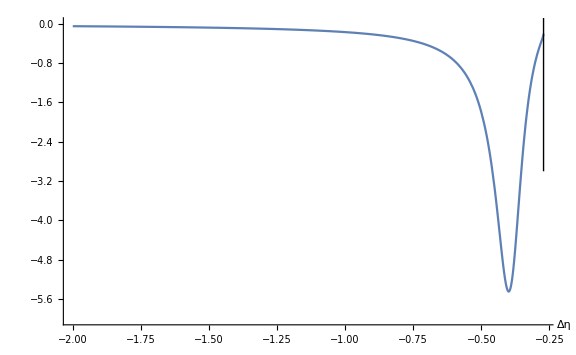

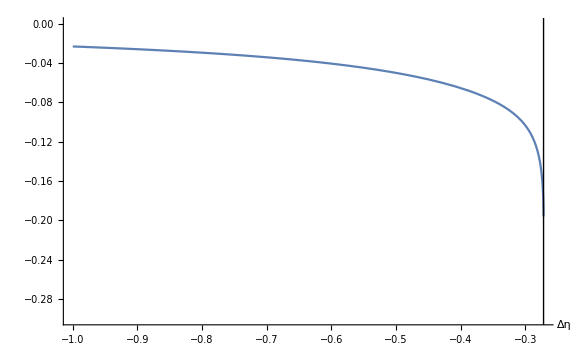

```mathematica
f2[x_]:= x/(2/3*(1+6.5*x)^2+1/3*(1-2.6*x)^2+2 Sqrt[2]/3*(1+6.5*x)*(1-2.6*x)*Sqrt[1-f[x]^2])
f3[x_]:= x/(2/3*(1+6.5*x)^2+1/3*(1-2.6*x)^2-2 Sqrt[2]/3*(1+6.5*x)*(1-2.6*x)*Sqrt[1-f[x]^2])
Manipulate[f3[x],{x,-5,0}]
Plot[{f2[x]},{x,-2,0},PlotRange->{-6,0},AxesLabel->{"Δη",""},ImageSize->Large,Epilog->{Line[{{r,-3},{r,5}}],Line[{{-1/6.5,-3},{-1/6.5,5}}]}](*,AxesStyle->Arrowheads[{0.0,0.05}]*)
Plot[{f3[x]},{x,-1,0},PlotRange->{-.3,0},AxesLabel->{"Δη",""},ImageSize->Large,Epilog->{Line[{{r,-3},{r,5}}],Line[{{-1/6.5,-3},{-1/6.5,5}}]}](*,AxesStyle->Arrowheads[{0.0,0.05}]*)
```

## Section- Lattice correspondence 1b.

```mathematica
(*Defining the refernce {ea_i} and deformed {em_i} basis vectors. *)
(*a0 is the dimensions of the Austenite primitive unit cell.*)
(*a is the dimensions of the Martensite primitive unit cell.*)
ea3[a0_,c0_,a_,b_,c_,β_]:={a0,-a0,0};
ea2[a0_,c0_,a_,b_,c_,β_]:={a0,a0,0};
ea1[a0_,c0_,a_,b_,c_,β_]:={0,0,c0};
em1[a0_,c0_,a_,b_,c_,β_]:={0,0,a};
em2[a0_,c0_,a_,b_,c_,β_]:={b/Sqrt[2],b/Sqrt[2],0};
em3[a0_,c0_,a_,b_,c_,β_]:={c*Sin[β]/Sqrt[2],-c*Sin[β]/Sqrt[2],c*Cos[β]};
{ea1[a0,c0,a,b,c,β],ea2[a0,c0,a,b,c,β],ea3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
{em1[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
```

(0 | a0 | a0
0 | a0 | -a0
c0 | 0 | 0)

(0 | b/(√2) | (c Sin[β])/(√2)
0 | b/(√2) | -(c Sin[β])/(√2)
a | 0 | c Cos[β])

```mathematica
(*Defining the reference dual and checking that its a dual. This defn works iff the vectors are mutually perpendicular to each other*)
rea1[a0_,c0_,a_,b_,c_,β_]:=1/(ea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β])ea1[a0,c0,a,b,c,β];
rea2[a0_,c0_,a_,b_,c_,β_]:=1/(ea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β])ea2[a0,c0,a,b,c,β];
rea3[a0_,c0_,a_,b_,c_,β_]:=1/(ea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β])ea3[a0,c0,a,b,c,β];
{{rea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea2[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea3[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]}}//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*Checking if the deofmred basis vectors were correctly identified. We know the dot products*)
{em1[a0,c0,a,b,c,β].em1[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β]}//Simplify
```

{a^2,0,a c Cos[β],b^2,0,c^2}

```mathematica
(*Writing out the expression for the 4 variants using Hanlin's expressions.*)
αHan1b[a0_,c0_,a_,b_,c_,β_]:=a/c0(*Han is suposed to stand for HAnlin's notation used in the Supplement of the Exploding and weeping paper*)
βHan1b[a0_,c0_,a_,b_,c_,β_]:=b/(Sqrt[2]*a0)
γHan1b[a0_,c0_,a_,b_,c_,β_]:=c/(Sqrt[2]*a0)
σHan1b[a0_,c0_,a_,b_,c_,β_]:=1/2*(βHan1b[a0,c0,a,b,c,β]+(γHan1b[a0,c0,a,b,c,β]*(γHan1b[a0,c0,a,b,c,β]+αHan1b[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[αHan1b[a0,c0,a,b,c,β]^2+γHan1b[a0,c0,a,b,c,β]^2+2*αHan1b[a0,c0,a,b,c,β]*γHan1b[a0,c0,a,b,c,β]*Sin[β]])
τHan1b[a0_,c0_,a_,b_,c_,β_]:=1/2*(βHan1b[a0,c0,a,b,c,β]-(γHan1b[a0,c0,a,b,c,β]*(γHan1b[a0,c0,a,b,c,β]+αHan1b[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[αHan1b[a0,c0,a,b,c,β]^2+γHan1b[a0,c0,a,b,c,β]^2+2*αHan1b[a0,c0,a,b,c,β]*γHan1b[a0,c0,a,b,c,β]*Sin[β]])
ρHan1b[a0_,c0_,a_,b_,c_,β_]:=(αHan1b[a0,c0,a,b,c,β]*γHan1b[a0,c0,a,b,c,β]*Cos[β])/(Sqrt[2]*Sqrt[αHan1b[a0,c0,a,b,c,β]^2+γHan1b[a0,c0,a,b,c,β]^2+2*αHan1b[a0,c0,a,b,c,β]*γHan1b[a0,c0,a,b,c,β]*Sin[β]])
ηHan1b[a0_,c0_,a_,b_,c_,β_]:=(αHan1b[a0,c0,a,b,c,β]*(αHan1b[a0,c0,a,b,c,β]+γHan1b[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[αHan1b[a0,c0,a,b,c,β]^2+γHan1b[a0,c0,a,b,c,β]^2+2*αHan1b[a0,c0,a,b,c,β]*γHan1b[a0,c0,a,b,c,β]*Sin[β]]
UI[a0_,c0_,a_,b_,c_,β_]:={{σHan1b[a0,c0,a,b,c,β],τHan1b[a0,c0,a,b,c,β],ρHan1b[a0,c0,a,b,c,β]},{τHan1b[a0,c0,a,b,c,β],σHan1b[a0,c0,a,b,c,β],-ρHan1b[a0,c0,a,b,c,β]},{ρHan1b[a0,c0,a,b,c,β],-ρHan1b[a0,c0,a,b,c,β],ηHan1b[a0,c0,a,b,c,β]}};
UII[a0_,c0_,a_,b_,c_,β_]:={{σHan1b[a0,c0,a,b,c,β],τHan1b[a0,c0,a,b,c,β],-ρHan1b[a0,c0,a,b,c,β]},{τHan1b[a0,c0,a,b,c,β],σHan1b[a0,c0,a,b,c,β],ρHan1b[a0,c0,a,b,c,β]},{-ρHan1b[a0,c0,a,b,c,β],ρHan1b[a0,c0,a,b,c,β],ηHan1b[a0,c0,a,b,c,β]}};
UIII[a0_,c0_,a_,b_,c_,β_]:={{σHan1b[a0,c0,a,b,c,β],-τHan1b[a0,c0,a,b,c,β],-ρHan1b[a0,c0,a,b,c,β]},{-τHan1b[a0,c0,a,b,c,β],σHan1b[a0,c0,a,b,c,β],-ρHan1b[a0,c0,a,b,c,β]},{-ρHan1b[a0,c0,a,b,c,β],-ρHan1b[a0,c0,a,b,c,β],ηHan1b[a0,c0,a,b,c,β]}};
UIV[a0_,c0_,a_,b_,c_,β_]:={{σHan1b[a0,c0,a,b,c,β],-τHan1b[a0,c0,a,b,c,β],ρHan1b[a0,c0,a,b,c,β]},{-τHan1b[a0,c0,a,b,c,β],σHan1b[a0,c0,a,b,c,β],ρHan1b[a0,c0,a,b,c,β]},{ρHan1b[a0,c0,a,b,c,β],ρHan1b[a0,c0,a,b,c,β],ηHan1b[a0,c0,a,b,c,β]}};
Manipulate[{"UI=",UI[a0,c0,a,b,c,β]//MatrixForm,"UII=",UII[a0,c0,a,b,c,β]//MatrixForm,"UIII=",UIII[a0,c0,a,b,c,β]//MatrixForm,"UIV=",UIV[a0,c0,a,b,c,β]//MatrixForm,"||UI-UI^T||=",Norm[UI[a0,c0,a,b,c,β]-Transpose[UI[a0,c0,a,b,c,β]]],"||UII-UII^T||=",Norm[UII[a0,c0,a,b,c,β]-Transpose[UII[a0,c0,a,b,c,β]]],"||UIII-UIII^T||=",Norm[UIII[a0,c0,a,b,c,β]-Transpose[UIII[a0,c0,a,b,c,β]]],"||UIV-UIV^T||=",Norm[UIV[a0,c0,a,b,c,β]-Transpose[UIV[a0,c0,a,b,c,β]]]},{{a0,1},1,2,0.01},{{c0,1.5},1,2,0.01},{{a,1.1},1,2,0.01},{{b,1.2},1,2,0.01},{{c,1.1},1,2,0.01},{{β,Pi/2+0.1},0,Pi,0.01}]
```

```mathematica
(*Determining the rotation for UII well under [110] loading*)
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIe)^2=",(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(U_IIIe)^2=",(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(U_IVe)^2=",(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(AU_I)=",A.UI[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

(U_Ie)^2=b^2/(2 a0^2)

(U_IIe)^2=b^2/(2 a0^2)

(U_IIIe)^2=c^2/(2 a0^2)

(U_IVe)^2=c^2/(2 a0^2)

(AU_I)=(b/(2 √2 a0) | b/(2 √2 a0) | 0
b/(2 √2 a0) | b/(2 √2 a0) | 0
0 | 0 | 0)

(AU_II)=(b/(2 √2 a0) | b/(2 √2 a0) | 0
b/(2 √2 a0) | b/(2 √2 a0) | 0
0 | 0 | 0)

(AU_III)=((c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | (c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | -(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
(c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | (c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | -(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
0 | 0 | 0)

(AU_IV)=((c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | (c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | (a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
(c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | (c (√2 c c0+2 a a0 Sin[β]))/(4 a0^2 c0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))) | (a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [110] loading*)
Clear[A,e,V,vm]
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

|U_IIIe|=c/(√2 a0)

|U_IVe|=c/(√2 a0)

|U_Ie|=b/(√2 a0)

|U_IIe|=b/(√2 a0)

```mathematica
(*Determining the Martensitic Well for [100] loading*)
(*Turns out min is achieved for all deformations that have $a/a_0$ in their 11 component.*)
Clear[A,e]
e:={1,0,0}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IIe)^2=",(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IIIe)^2=",(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IVe)^2=",(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(AU_I)=",A.UI[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(U_Ie)^2=(b^2+c^2)/(4 a0^2)

(U_IIe)^2=(b^2+c^2)/(4 a0^2)

(U_IIIe)^2=(b^2+c^2)/(4 a0^2)

(U_IVe)^2=(b^2+c^2)/(4 a0^2)

(AU_I)=(1/2 (b/(√2 a0)+(c (c/(√2 a0)+(a Sin[β])/c0))/(a0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0)))) | (√2 b-(2 c (c/(√2 a0)+(a Sin[β])/c0))/(√(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))))/(4 a0) | (a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
0 | 0 | 0
0 | 0 | 0)

(AU_II)=(1/2 (b/(√2 a0)+(c (c/(√2 a0)+(a Sin[β])/c0))/(a0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0)))) | (√2 b-(2 c (c/(√2 a0)+(a Sin[β])/c0))/(√(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0))))/(4 a0) | -(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
0 | 0 | 0
0 | 0 | 0)

(AU_III)=(1/2 (b/(√2 a0)+(c (c/(√2 a0)+(a Sin[β])/c0))/(a0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0)))) | 1/2 (-b/(√2 a0)+(c (c/(√2 a0)+(a Sin[β])/c0))/(a0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0)))) | -(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
0 | 0 | 0
0 | 0 | 0)

(AU_IV)=(1/2 (b/(√2 a0)+(c (c/(√2 a0)+(a Sin[β])/c0))/(a0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0)))) | 1/2 (-b/(√2 a0)+(c (c/(√2 a0)+(a Sin[β])/c0))/(a0 √(c^2/a0^2+(2 a^2)/c0^2+(2 √2 a c Sin[β])/(a0 c0)))) | (a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0)))
0 | 0 | 0
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [100] loading*)
Clear[A,e,V,vm]
e={1,0,0};
A=Outer[Times,e,e];
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

|U_IIIe|=(√(b^2+c^2))/(2 a0)

|U_IVe|=(√(b^2+c^2))/(2 a0)

|U_Ie|=(√(b^2+c^2))/(2 a0)

|U_IIe|=(√(b^2+c^2))/(2 a0)

```mathematica
(*Determining the Martensitic Well for [001] loading*)
(*Turns out min is achieved at all of them*)
Clear[A,e]
e:={0,0,1}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIe)^2=",(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIIe)^2=",(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IVe)^2=",(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(AU_I)=",A.UI[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(R(θ,e1+e2)A)=",RotationMatrix[μ,{1,0,0}].A//Simplify//PowerExpand//MatrixForm]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(U_Ie)^2=a^2/c0^2

(U_IIe)^2=a^2/c0^2

(U_IIIe)^2=a^2/c0^2

(U_IVe)^2=a^2/c0^2

(AU_I)=(0 | 0 | 0
0 | 0 | 0
(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | -(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | (a (2 a a0+√2 c c0 Sin[β]))/(a0 c0^2 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))))

(AU_II)=(0 | 0 | 0
0 | 0 | 0
-(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | (a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | (a (2 a a0+√2 c c0 Sin[β]))/(a0 c0^2 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))))

(AU_III)=(0 | 0 | 0
0 | 0 | 0
-(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | -(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | (a (2 a a0+√2 c c0 Sin[β]))/(a0 c0^2 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))))

(AU_IV)=(0 | 0 | 0
0 | 0 | 0
(a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | (a c Cos[β])/(a0 c0 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))) | (a (2 a a0+√2 c c0 Sin[β]))/(a0 c0^2 √((2 c^2)/a0^2+(4 a^2)/c0^2+(4 √2 a c Sin[β])/(a0 c0))))

(R(θ,e1+e2)A)=(0 | 0 | 0
0 | 0 | -Sin[μ]
0 | 0 | Cos[μ])

```mathematica
(*The LHS of the Claussius Clayperon equation for [001] loading*)
Clear[A,e,V,vm]
e={0,0,1};
A=Outer[Times,e,e];
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

|U_IIIe|=a/c0

|U_IVe|=a/c0

|U_Ie|=a/c0

|U_IIe|=a/c0

```mathematica
(*Determinant of the Tensors for Pressure loading device calculation*)
Print["det UI=",Det[UI[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UII=",Det[UII[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIII=",Det[UIII[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIV=",Det[UIV[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
```

det UI=(a b c Sin[β])/(2 a0^2 c0)

det UII=(a b c Sin[β])/(2 a0^2 c0)

det UIII=(a b c Sin[β])/(2 a0^2 c0)

det UIV=(a b c Sin[β])/(2 a0^2 c0)

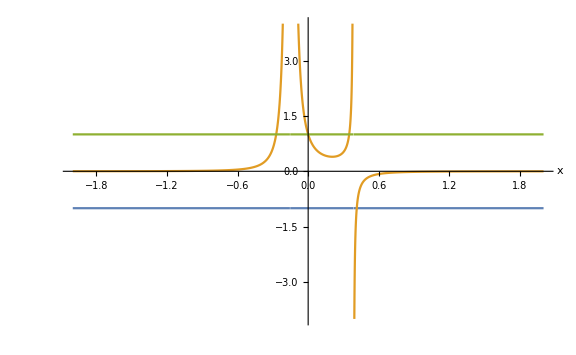

```mathematica
(*Checking if a solution exists. We equate the Claussius Clayperon equation for [100] and [001] loading as they have the same change in entropy. We test if a solution cna exist*)
f[x_,w_,β_]:=1/((1+6.5*x)^2*(1-2.6*x))
Plot[{-1,f[x],1},{x,-2,2},AxesLabel->Automatic,ImageSize->Large]
```

## Section- Lattice correspondence 2.

```mathematica
(*Defining the refernce {ea_i} and deformed {em_i} basis vectors. *)
(*a0 is the dimensions of the Austenite primitive unit cell.*)
(*a is the dimensions of the Martensite primitive unit cell.*)
ea3[a0_,c0_,a_,b_,c_,β_]:={a0,-a0,0};
ea1[a0_,c0_,a_,b_,c_,β_]:={a0,a0,0};
ea2[a0_,c0_,a_,b_,c_,β_]:={0,0,c0};
em1[a0_,c0_,a_,b_,c_,β_]:={a/Sqrt[2],a/Sqrt[2],0};
em2[a0_,c0_,a_,b_,c_,β_]:={0,0,b};
em3[a0_,c0_,a_,b_,c_,β_]:={c*(Cos[β]+Sin[β])/Sqrt[2],c*(Cos[β]-Sin[β])/Sqrt[2],0};
{ea1[a0,c0,a,b,c,β],ea2[a0,c0,a,b,c,β],ea3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
{em1[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
```

(a0 | 0 | a0
a0 | 0 | -a0
0 | c0 | 0)

(a/(√2) | 0 | (c (Cos[β]+Sin[β]))/(√2)
a/(√2) | 0 | (c (Cos[β]-Sin[β]))/(√2)
0 | b | 0)

```mathematica
(*Defining the reference dual and checking that its a dual. This defn works iff the vectors are mutually perpendicular to each other*)
rea1[a0_,c0_,a_,b_,c_,β_]:=1/(ea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β])ea1[a0,c0,a,b,c,β];
rea2[a0_,c0_,a_,b_,c_,β_]:=1/(ea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β])ea2[a0,c0,a,b,c,β];
rea3[a0_,c0_,a_,b_,c_,β_]:=1/(ea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β])ea3[a0,c0,a,b,c,β];
{{rea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea2[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea3[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]}}//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*Checking if the deofmred basis vectors were correctly identified. We know the dot products*)
{em1[a0,c0,a,b,c,β].em1[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β]}//Simplify
```

{a^2,0,a c Cos[β],b^2,0,c^2}

```mathematica
(*Writing out the expression for the 4 variants using Hanlin's expressions.*)
αHan2[a0_,c0_,a_,b_,c_,β_]:=a/(Sqrt[2]*a0)(*Han is suposed to stand for Hanlin's notation used in the Supplement of the Exploding and weeping paper*)
βHan2[a0_,c0_,a_,b_,c_,β_]:=b/c0
γHan2[a0_,c0_,a_,b_,c_,β_]:=c/(Sqrt[2]*a0)
ξHan2[a0_,c0_,a_,b_,c_,β_]:=(αHan2[a0,c0,a,b,c,β]^2+γHan2[a0,c0,a,b,c,β]^2+2*αHan2[a0,c0,a,b,c,β]*γHan2[a0,c0,a,b,c,β]*(Sin[β]+Cos[β]))/(2*Sqrt[αHan2[a0,c0,a,b,c,β]^2+γHan2[a0,c0,a,b,c,β]^2+2*αHan2[a0,c0,a,b,c,β]*γHan2[a0,c0,a,b,c,β]*Sin[β]])
ωHan2[a0_,c0_,a_,b_,c_,β_]:=(αHan2[a0,c0,a,b,c,β]^2+γHan2[a0,c0,a,b,c,β]^2+2*αHan2[a0,c0,a,b,c,β]*γHan2[a0,c0,a,b,c,β]*(Sin[β]-Cos[β]))/(2*Sqrt[αHan2[a0,c0,a,b,c,β]^2+γHan2[a0,c0,a,b,c,β]^2+2*αHan2[a0,c0,a,b,c,β]*γHan2[a0,c0,a,b,c,β]*Sin[β]])
κHan2[a0_,c0_,a_,b_,c_,β_]:=(αHan2[a0,c0,a,b,c,β]^2-γHan2[a0,c0,a,b,c,β]^2)/(2*Sqrt[αHan2[a0,c0,a,b,c,β]^2+γHan2[a0,c0,a,b,c,β]^2+2*αHan2[a0,c0,a,b,c,β]*γHan2[a0,c0,a,b,c,β]*Sin[β]])
UI[a0_,c0_,a_,b_,c_,β_]:={{ξHan2[a0,c0,a,b,c,β],κHan2[a0,c0,a,b,c,β],0},{κHan2[a0,c0,a,b,c,β],ωHan2[a0,c0,a,b,c,β],0},{0,0,βHan2[a0,c0,a,b,c,β]}};
UII[a0_,c0_,a_,b_,c_,β_]:={{ωHan2[a0,c0,a,b,c,β],κHan2[a0,c0,a,b,c,β],0},{κHan2[a0,c0,a,b,c,β],ξHan2[a0,c0,a,b,c,β],0},{0,0,βHan2[a0,c0,a,b,c,β]}};
UIII[a0_,c0_,a_,b_,c_,β_]:={{ξHan2[a0,c0,a,b,c,β],-κHan2[a0,c0,a,b,c,β],0},{-κHan2[a0,c0,a,b,c,β],ωHan2[a0,c0,a,b,c,β],0},{0,0,βHan2[a0,c0,a,b,c,β]}};
UIV[a0_,c0_,a_,b_,c_,β_]:={{ωHan2[a0,c0,a,b,c,β],-κHan2[a0,c0,a,b,c,β],0},{-κHan2[a0,c0,a,b,c,β],ξHan2[a0,c0,a,b,c,β],0},{0,0,βHan2[a0,c0,a,b,c,β]}};
Manipulate[{"UI=",UI[a0,c0,a,b,c,β]//MatrixForm,"UII=",UII[a0,c0,a,b,c,β]//MatrixForm,"UIII=",UIII[a0,c0,a,b,c,β]//MatrixForm,"UIV=",UIV[a0,c0,a,b,c,β]//MatrixForm,"||UI-UI^T||=",Norm[UI[a0,c0,a,b,c,β]-Transpose[UI[a0,c0,a,b,c,β]]],"||UII-UII^T||=",Norm[UII[a0,c0,a,b,c,β]-Transpose[UII[a0,c0,a,b,c,β]]],"||UIII-UIII^T||=",Norm[UIII[a0,c0,a,b,c,β]-Transpose[UIII[a0,c0,a,b,c,β]]],"||UIV-UIV^T||=",Norm[UIV[a0,c0,a,b,c,β]-Transpose[UIV[a0,c0,a,b,c,β]]]},{{a0,1},1,2,0.01},{{c0,1.5},1,2,0.01},{{a,1.1},1,2,0.01},{{b,1.2},1,2,0.01},{{c,1.1},1,2,0.01},{{β,Pi/2+0.1},0,Pi,0.01}]
Print["UI=",{{ξHan2,κHan2,0},{κHan2,ωHan2,0},{0,0,βHan2}}//MatrixForm]
Print["UII=",{{ωHan2,κHan2,0},{κHan2,ξHan2,0},{0,0,βHan2}}//MatrixForm]
Print["UIII=",{{ξHan2,-κHan2,0},{-κHan2,ωHan2,0},{0,0,βHan2}}//MatrixForm]
Print["UIV=",{{ωHan2,-κHan2,0},{-κHan2,ξHan2,0},{0,0,βHan2}}//MatrixForm]
```

UI=(ξHan2 | κHan2 | 0
κHan2 | ωHan2 | 0
0 | 0 | βHan2)

UII=(ωHan2 | κHan2 | 0
κHan2 | ξHan2 | 0
0 | 0 | βHan2)

UIII=(ξHan2 | -κHan2 | 0
-κHan2 | ωHan2 | 0
0 | 0 | βHan2)

UIV=(ωHan2 | -κHan2 | 0
-κHan2 | ξHan2 | 0
0 | 0 | βHan2)

```mathematica
(*Determining the rotation for UII well under [110] loading*)
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)//Simplify]
Print["(U_IIe)^2=",(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(U_IIIe)^2=",(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IVe)^2=",(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(AU_I)=",A.UI[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*c0,Subscript[γ̂, r]*Sqrt[2]*a0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*c0,Subscript[γ̂, r]*Sqrt[2]*a0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*c0,Subscript[γ̂, r]*Sqrt[2]*a0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*c0,Subscript[γ̂, r]*Sqrt[2]*a0,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

(U_Ie)^2=a^2/(2 a0^2)

(U_IIe)^2=a^2/(2 a0^2)

(U_IIIe)^2=c^2/(2 a0^2)

(U_IVe)^2=c^2/(2 a0^2)

(AU_I)=(((α̂)_r ((α̂)_r+(Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((α̂)_r ((α̂)_r+(-Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
((α̂)_r ((α̂)_r+(Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((α̂)_r ((α̂)_r+(-Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
0 | 0 | 0)

(AU_II)=(((α̂)_r ((α̂)_r+(-Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((α̂)_r ((α̂)_r+(Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
((α̂)_r ((α̂)_r+(-Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((α̂)_r ((α̂)_r+(Cos[β]+Sin[β]) (γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
0 | 0 | 0)

(AU_III)=(((γ̂)_r ((Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((γ̂)_r ((-Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
((γ̂)_r ((Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((γ̂)_r ((-Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
0 | 0 | 0)

(AU_IV)=(((γ̂)_r ((-Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((γ̂)_r ((Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
((γ̂)_r ((-Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | ((γ̂)_r ((Cos[β]+Sin[β]) (α̂)_r+(γ̂)_r))/(2 √((α̂)_r^2+2 Sin[β] (α̂)_r (γ̂)_r+(γ̂)_r^2)) | 0
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [110] loading*)
Clear[A,e,V,vm]
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

|U_IIIe|=c/(√2 a0)

|U_IVe|=c/(√2 a0)

|U_Ie|=a/(√2 a0)

|U_IIe|=a/(√2 a0)

```mathematica
(*Determining the Martensitic Well for [100] loading*)
(*Turns out min is achieved for all deformations that have $a/a_0$ in their 11 component.*)
Clear[A,e]
e:={1,0,0}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IIe)^2=",(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IIIe)^2=",(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IVe)^2=",(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(AU_I)=",A.UI[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(U_Ie)^2=(a^2+c^2+2 a c Cos[β])/(4 a0^2)

(U_IIe)^2=(a^2+c^2-2 a c Cos[β])/(4 a0^2)

(U_IIIe)^2=(a^2+c^2+2 a c Cos[β])/(4 a0^2)

(U_IVe)^2=(a^2+c^2-2 a c Cos[β])/(4 a0^2)

(AU_I)=((a^2+c^2+2 a c Cos[β]+2 a c Sin[β])/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | (a^2-c^2)/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | 0
0 | 0 | 0
0 | 0 | 0)

(AU_II)=((a^2+c^2-2 a c Cos[β]+2 a c Sin[β])/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | (a^2-c^2)/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | 0
0 | 0 | 0
0 | 0 | 0)

(AU_III)=((a^2+c^2+2 a c Cos[β]+2 a c Sin[β])/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | (-a^2+c^2)/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | 0
0 | 0 | 0
0 | 0 | 0)

(AU_IV)=((a^2+c^2-2 a c Cos[β]+2 a c Sin[β])/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | (-a^2+c^2)/(2 √2 a0 √(a^2+c^2+2 a c Sin[β])) | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [100] loading*)
Clear[A,e,V,vm]
e={1,0,0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

|U_IIIe|=(√(a^2+c^2+2 a c Cos[β]))/(2 a0)

|U_IVe|=(√(a^2+c^2-2 a c Cos[β]))/(2 a0)

|U_Ie|=(√(a^2+c^2+2 a c Cos[β]))/(2 a0)

|U_IIe|=(√(a^2+c^2-2 a c Cos[β]))/(2 a0)

```mathematica
(*Determining the Martensitic Well for [001] loading*)
(*Turns out min is achieved at all of them*)
Clear[A,e]
e:={0,0,1}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_Ie)^2=",(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIe)^2=",(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIIe)^2=",(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IVe)^2=",(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(AU_I)=",A.UI[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_II)=",A.UII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_III)=",A.UIII[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IV)=",A.UIV[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(U_Ie)^2=b^2/c0^2

(U_IIe)^2=b^2/c0^2

(U_IIIe)^2=b^2/c0^2

(U_IVe)^2=b^2/c0^2

(AU_I)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | b/c0)

(AU_II)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | b/c0)

(AU_III)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | b/c0)

(AU_IV)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | b/c0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [001] loading*)
Clear[A,e,V,vm]
e={0,0,1};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIe|=",Sqrt[(UIII[a0,c0,a,b,c,β].e).(UIII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVe|=",Sqrt[(UIV[a0,c0,a,b,c,β].e).(UIV[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_Ie|=",Sqrt[(UI[a0,c0,a,b,c,β].e).(UI[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIe|=",Sqrt[(UII[a0,c0,a,b,c,β].e).(UII[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

|U_IIIe|=b/c0

|U_IVe|=b/c0

|U_Ie|=b/c0

|U_IIe|=b/c0

```mathematica
(*Determinant of the Tensors for Pressure loading device calculation*)
Print["det UI=",Det[UI[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UII=",Det[UII[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIII=",Det[UIII[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIV=",Det[UIV[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
```

det UI=(a b c Sin[β])/(2 a0^2 c0)

det UII=(a b c Sin[β])/(2 a0^2 c0)

det UIII=(a b c Sin[β])/(2 a0^2 c0)

det UIV=(a b c Sin[β])/(2 a0^2 c0)

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-0.029112<y<0

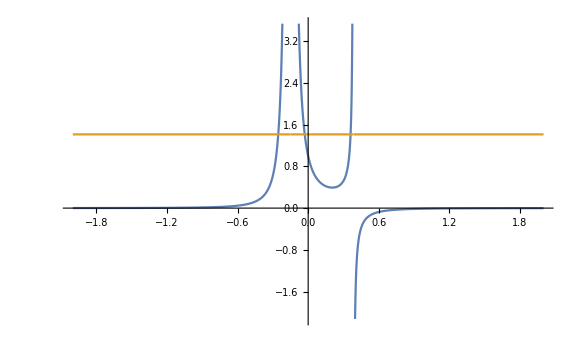

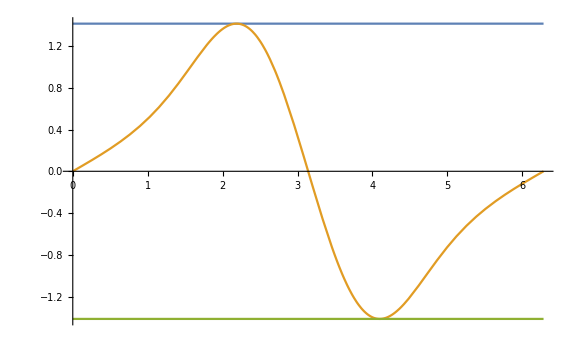

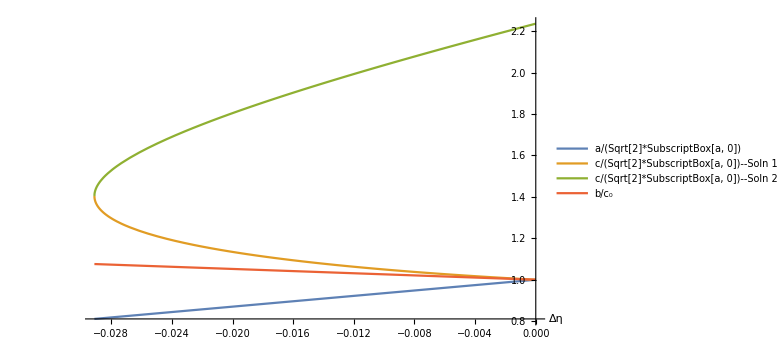

```mathematica
(*Checking if a solution exists. We equate the Claussius Clayperon equation for [100] and [001] loading as they have the same change in entropy. We test if a solution cna exist*)
f1[x_]:=1/((1+6.5*x)^2*(1-2.6*x))
f2[y_]:=Sin[y]/(Cos[y]+Sqrt[1+Cos[y]^2])
f31[z_]:=(1+z^2+2*z^2*Sqrt[2-z^2])/(1+4*z^2)(*Cos^2 β soln 1*)
f32[z_]:=(1+z^2-2*z^2*Sqrt[2-z^2])/(1+4*z^2)(*Cos^2 β soln 2*)
Reduce[{-Sqrt[2]<f1[y]<Sqrt[2],y<0,1+6.5*y>0},y](*This is the solution to the equation with *)
Plot[{f1[x],Sqrt[2]},{x,-2,2},ImageSize->Large]
Plot[{Sqrt[2],f2[y],-Sqrt[2]},{y,0,2*Pi}]
Plot[{1+6.5*x,((1+6.5*x)*Sqrt[1+4*f1[x]^2])/Sqrt[3+2*Sqrt[2-f1[x]^2]],((1+6.5*x)*Sqrt[1+4*f1[x]^2])/Sqrt[3-2*Sqrt[2-f1[x]^2]],1-2.6*x},{x,-0.02911201647890081,0},PlotLegends->{"a/(Sqrt[2]*SubscriptBox[a, 0])","c/(Sqrt[2]*SubscriptBox[a, 0])--Soln 1","c/(Sqrt[2]*SubscriptBox[a, 0])--Soln 2","b/c_0"},AxesLabel->{"Δη",""},ImageSize->Large](*HEre we plot the lattice parameter ratio's in terms of the Δη*)
(*plot2=Plot[{(1+6.5*x)*f1[x]/□},{x,-2,0}](*HEre we plot the lattice parameter ratio's in terms of the Δη*)*)
```

Δη=-0.014556

a/(Sqrt[2]*SubscriptBox[a, 0])=0.905386

c/(Sqrt[2]*SubscriptBox[a, 0])--Soln 1=1.08166

c/(Sqrt[2]*SubscriptBox[a, 0])--Soln 2=1.93607

b/a_0=1.03785

dσ_111/dθ_c=Δη/(Sqrt[FractionBox[2 SuperscriptBox[(1 + 6.5*Δη), 2] + (1 - 2.6  Δη), 3]] - 1)=0.263151

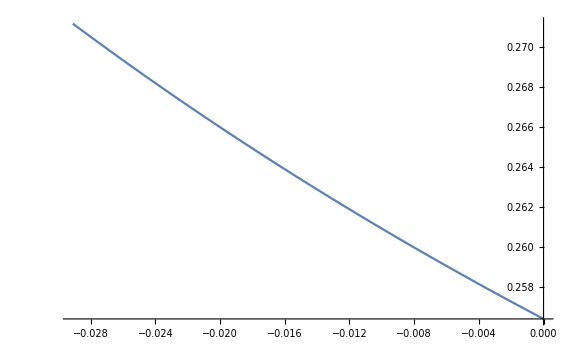

```mathematica
(*Prediction 1- Average LAttice parameter values*)
xx=-0.02911201647890081/2;
Print["Δη=",xx]
Print["a/(Sqrt[2]*SubscriptBox[a, 0])=",1+6.5*xx]
Print["c/(Sqrt[2]*SubscriptBox[a, 0])--Soln 1=",((1+6.5*xx)*Sqrt[1+4*f1[xx]^2])/Sqrt[3+2*Sqrt[2-f1[xx]^2]]]
Print["c/(Sqrt[2]*SubscriptBox[a, 0])--Soln 2=",((1+6.5*xx)*Sqrt[1+4*f1[xx]^2])/Sqrt[3-2*Sqrt[2-f1[xx]^2]]]
Print["b/a_0=",1-2.6*xx]
Print["dσ_111/dθ_c=Δη/(Sqrt[FractionBox[2 SuperscriptBox[(1 + 6.5*Δη), 2] + (1 - 2.6  Δη), 3]] - 1)=",xx/(Sqrt[(2(1+6.5*xx)^2+(1-2.6xx))/3]-1)]
Plot[x/(Sqrt[(2(1+6.5*x)^2+(1-2.6x))/3]-1),{x,-0.02911201647890081,0},ImageSize->Large]
```

```mathematica
(*Prediction 2 - Predicting the direction of maximum increase of Tc. *)
ê:={1/Sqrt[3],1/Sqrt[3],1/Sqrt[3]}
(UI[a0,c0,a,b,c,β].ê).(UI[a0,c0,a,b,c,β].ê)//Simplify
(UII[a0,c0,a,b,c,β].ê).(UII[a0,c0,a,b,c,β].ê)//Simplify
(UIII[a0,c0,a,b,c,β].ê).(UIII[a0,c0,a,b,c,β].ê)//Simplify
(UIV[a0,c0,a,b,c,β].ê).(UIV[a0,c0,a,b,c,β].ê)//Simplify
(*Eigenvalues[UI[a0,c0,a,b,c,β]]//PowerExpand//TrigReduce//Simplify
Eigenvectors[UI[a0,c0,a,b,c,β]]//PowerExpand//TrigReduce//Simplify*)
```

1/3 (a^2/a0^2+b^2/c0^2)

1/3 (a^2/a0^2+b^2/c0^2)

1/3 (c^2/a0^2+b^2/c0^2)

1/3 (c^2/a0^2+b^2/c0^2)

## Section- Lattice correspondence 3.

```mathematica
(*Defining the refernce {ea_i} and deformed {em_i} basis vectors. *)
(*a0 is the dimensions of the Austenite primitive unit cell.*)
(*a is the dimensions of the Martensite primitive unit cell.*)
ea1C3[a0_,c0_,a_,b_,c_,β_]:={a0,-a0,0};
ea2C3[a0_,c0_,a_,b_,c_,β_]:={a0,a0,0};
ea3C3[a0_,c0_,a_,b_,c_,β_]:={0,0,c0};
em1C3[a0_,c0_,a_,b_,c_,β_]:=1/Sqrt[2]*{b,-a,0};
em2C3[a0_,c0_,a_,b_,c_,β_]:=1/Sqrt[2]*{b,a,0};
em3C3[a0_,c0_,a_,b_,c_,β_]:={c*Cos[β],0,c*Sin[β]};
{ea1C3[a0,c0,a,b,c,β],ea2C3[a0,c0,a,b,c,β],ea3C3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
{em1C3[a0,c0,a,b,c,β],em2C3[a0,c0,a,b,c,β],em3C3[a0,c0,a,b,c,β]}//Transpose//MatrixForm
```

(a0 | a0 | 0
-a0 | a0 | 0
0 | 0 | c0)

(b/(√2) | b/(√2) | c Cos[β]
-a/(√2) | a/(√2) | 0
0 | 0 | c Sin[β])

```mathematica
(*Defining the reference dual and checking that its a dual. This defn works iff the vectors are mutually perpendicular to each other*)
rea1[a0_,c0_,a_,b_,c_,β_]:=1/(ea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β])ea1[a0,c0,a,b,c,β];
rea2[a0_,c0_,a_,b_,c_,β_]:=1/(ea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β])ea2[a0,c0,a,b,c,β];
rea3[a0_,c0_,a_,b_,c_,β_]:=1/(ea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β])ea3[a0,c0,a,b,c,β];
{{rea1[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea1[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea2[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea2[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]},{rea3[a0,c0,a,b,c,β].ea1[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea2[a0,c0,a,b,c,β],rea3[a0,c0,a,b,c,β].ea3[a0,c0,a,b,c,β]}}//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

```mathematica
(*Checking if the deofmred basis vectors were correctly identified. We know the dot products*)
{em1[a0,c0,a,b,c,β].em1[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em1[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em2[a0,c0,a,b,c,β],em2[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β],em3[a0,c0,a,b,c,β].em3[a0,c0,a,b,c,β]}//Simplify
```

{a^2,0,a c Cos[β],b^2,0,c^2}

```mathematica
(*Writing out the expression for the 4 variants using Hanlin's expressions.*)
α3[a0_,c0_,a_,b_,c_,β_]:=a/(Sqrt[2]*a0)(*Han is suposed to stand for Hanlin's notation used in the Supplement of the Exploding and weeping paper*)
β3[a0_,c0_,a_,b_,c_,β_]:=b/(Sqrt[2]*a0)
γ3[a0_,c0_,a_,b_,c_,β_]:=c/c0
σ3[a0_,c0_,a_,b_,c_,β_]:=(β3[a0,c0,a,b,c,β]*(β3[a0,c0,a,b,c,β]+γ3[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[β3[a0,c0,a,b,c,β]^2+γ3[a0,c0,a,b,c,β]^2+2*β3[a0,c0,a,b,c,β]*γ3[a0,c0,a,b,c,β]*Sin[β]]
(*τ3[a0_,c0_,a_,b_,c_,β_]:=(β3[a0,c0,a,b,c,β]*γ3[a0,c0,a,b,c,β]*Cos[β])/Sqrt[β3[a0,c0,a,b,c,β]^2+γ3[a0,c0,a,b,c,β]^2+2*β3[a0,c0,a,b,c,β]*γ3[a0,c0,a,b,c,β]*Sin[β]]*)
ρ3[a0_,c0_,a_,b_,c_,β_]:=(β3[a0,c0,a,b,c,β]*γ3[a0,c0,a,b,c,β]*Cos[β])/Sqrt[β3[a0,c0,a,b,c,β]^2+γ3[a0,c0,a,b,c,β]^2+2*β3[a0,c0,a,b,c,β]*γ3[a0,c0,a,b,c,β]*Sin[β]]
η3[a0_,c0_,a_,b_,c_,β_]:=(γ3[a0,c0,a,b,c,β]*(γ3[a0,c0,a,b,c,β]+β3[a0,c0,a,b,c,β]*Sin[β]))/Sqrt[β3[a0,c0,a,b,c,β]^2+γ3[a0,c0,a,b,c,β]^2+2*β3[a0,c0,a,b,c,β]*γ3[a0,c0,a,b,c,β]*Sin[β]]
UIC3[a0_,c0_,a_,b_,c_,β_]:={{σ3[a0,c0,a,b,c,β],0,ρ3[a0,c0,a,b,c,β]},{0,α3[a0,c0,a,b,c,β],0},{ρ3[a0,c0,a,b,c,β],0,η3[a0,c0,a,b,c,β]}};
UIIC3[a0_,c0_,a_,b_,c_,β_]:={{α3[a0,c0,a,b,c,β],0,0},{0,σ3[a0,c0,a,b,c,β],-ρ3[a0,c0,a,b,c,β]},{0,-ρ3[a0,c0,a,b,c,β],η3[a0,c0,a,b,c,β]}};
UIIIC3[a0_,c0_,a_,b_,c_,β_]:={{σ3[a0,c0,a,b,c,β],0,-ρ3[a0,c0,a,b,c,β]},{0,α3[a0,c0,a,b,c,β],0},{-ρ3[a0,c0,a,b,c,β],0,η3[a0,c0,a,b,c,β]}};
UIVC3[a0_,c0_,a_,b_,c_,β_]:={{α3[a0,c0,a,b,c,β],0,0},{0,σ3[a0,c0,a,b,c,β],ρ3[a0,c0,a,b,c,β]},{0,ρ3[a0,c0,a,b,c,β],η3[a0,c0,a,b,c,β]}};
Manipulate[{"UI=",UI[a0,c0,a,b,c,β]//MatrixForm,"UII=",UII[a0,c0,a,b,c,β]//MatrixForm,"UIII=",UIII[a0,c0,a,b,c,β]//MatrixForm,"UIV=",UIV[a0,c0,a,b,c,β]//MatrixForm,"||UI-UI^T||=",Norm[UI[a0,c0,a,b,c,β]-Transpose[UI[a0,c0,a,b,c,β]]],"||UII-UII^T||=",Norm[UII[a0,c0,a,b,c,β]-Transpose[UII[a0,c0,a,b,c,β]]],"||UIII-UIII^T||=",Norm[UIII[a0,c0,a,b,c,β]-Transpose[UIII[a0,c0,a,b,c,β]]],"||UIV-UIV^T||=",Norm[UIV[a0,c0,a,b,c,β]-Transpose[UIV[a0,c0,a,b,c,β]]]},{{a0,1},1,2,0.01},{{c0,1.5},1,2,0.01},{{a,1.1},1,2,0.01},{{b,1.2},1,2,0.01},{{c,1.1},1,2,0.01},{{β,Pi/2+0.1},0,Pi,0.01}]
```

```mathematica
(σ3[a0,c0,a,b,c,β]^2+α3[a0,c0,a,b,c,β]^2+ρ3[a0,c0,a,b,c,β]^2)/2//Simplify
```

(a^2+b^2)/(4 a0^2)

```mathematica
(*Determining the rotation for UII well under [110] loading*)
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_IC3e)^2=",(UIC3[a0,c0,a,b,c,β].e).(UIC3[a0,c0,a,b,c,β].e)//Simplify]
Print["(U_IIC3e)^2=",(UIIC3[a0,c0,a,b,c,β].e).(UIIC3[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(U_IIIC3e)^2=",(UIIIC3[a0,c0,a,b,c,β].e).(UIIIC3[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IVC3e)^2=",(UIVC3[a0,c0,a,b,c,β].e).(UIVC3[a0,c0,a,b,c,β].e)//PowerExpand//TrigExpand//Simplify]
Print["(AU_IC3)=",A.UIC3[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*Sqrt[2]*a0,Subscript[γ̂, r]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IIC3)=",A.UIIC3[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*Sqrt[2]*a0,Subscript[γ̂, r]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IIIC3)=",A.UIIIC3[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*Sqrt[2]*a0,Subscript[γ̂, r]*c0,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IVC3)=",A.UIVC3[a0,c0,Subscript[α̂, r]*Sqrt[2]*a0,Subscript[β̂, r]*Sqrt[2]*a0,Subscript[γ̂, r]*c0,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

(U_IC3e)^2=(a^2+b^2)/(4 a0^2)

(U_IIC3e)^2=(a^2+b^2)/(4 a0^2)

(U_IIIC3e)^2=(a^2+b^2)/(4 a0^2)

(U_IVC3e)^2=(a^2+b^2)/(4 a0^2)

(AU_IC3)=(((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | ((α̂)_-0.271625)/2 | (Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | ((α̂)_-0.271625)/2 | (Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
0 | 0 | 0)

(AU_IIC3)=(((α̂)_-0.271625)/2 | ((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | -(Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
((α̂)_-0.271625)/2 | ((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | -(Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
0 | 0 | 0)

(AU_IIIC3)=(((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | ((α̂)_-0.271625)/2 | -(Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | ((α̂)_-0.271625)/2 | -(Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
0 | 0 | 0)

(AU_IVC3)=(((α̂)_-0.271625)/2 | ((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | (Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
((α̂)_-0.271625)/2 | ((β̂)_-0.271625 ((β̂)_-0.271625+Sin[β] (γ̂)_-0.271625))/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2)) | (Cos[β] (β̂)_-0.271625 (γ̂)_-0.271625)/(2 √((β̂)_-0.271625^2+2 Sin[β] (β̂)_-0.271625 (γ̂)_-0.271625+(γ̂)_-0.271625^2))
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [110] loading*)
Clear[A,e,V,vm]
e={1/Sqrt[2],1/Sqrt[2],0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIC3e|=",Sqrt[(UIIIC3[a0,c0,a,b,c,β].e).(UIIIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVC3e|=",Sqrt[(UIVC3[a0,c0,a,b,c,β].e).(UIVC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IC3e|=",Sqrt[(UIC3[a0,c0,a,b,c,β].e).(UIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIC3e|=",Sqrt[(UIIC3[a0,c0,a,b,c,β].e).(UIIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(1/2 | 1/2 | 0
1/2 | 1/2 | 0
0 | 0 | 0)

|U_IIIC3e|=(√(a^2+b^2))/(2 a0)

|U_IVC3e|=(√(a^2+b^2))/(2 a0)

|U_IC3e|=(√(a^2+b^2))/(2 a0)

|U_IIC3e|=(√(a^2+b^2))/(2 a0)

```mathematica
(*Determining the Martensitic Well for [100] loading*)
(*Turns out min is achieved for all deformations that have $a/a_0$ in their 11 component.*)
Clear[A,e]
e:={1,0,0}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_IC3e)^2=",(UIC3[a0,c0,a,b,c,β].e).(UIC3[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IIC3e)^2=",(UIIC3[a0,c0,a,b,c,β].e).(UIIC3[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IIIC3e)^2=",(UIIIC3[a0,c0,a,b,c,β].e).(UIIIC3[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(U_IVC3e)^2=",(UIVC3[a0,c0,a,b,c,β].e).(UIVC3[a0,c0,a,b,c,β].e)//PowerExpand//TrigReduce//Simplify]
Print["(AU_IC3)=",A.UIC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IIC3)=",A.UIIC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IIIC3)=",A.UIIIC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IVC3)=",A.UIVC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(U_IC3e)^2=b^2/(2 a0^2)

(U_IIC3e)^2=a^2/(2 a0^2)

(U_IIIC3e)^2=b^2/(2 a0^2)

(U_IVC3e)^2=a^2/(2 a0^2)

(AU_IC3)=((b (√2 b c0+2 a0 c Sin[β]))/(2 a0^2 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0))) | 0 | (b c Cos[β])/(a0 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0)))
0 | 0 | 0
0 | 0 | 0)

(AU_IIC3)=(a/(√2 a0) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

(AU_IIIC3)=((b (√2 b c0+2 a0 c Sin[β]))/(2 a0^2 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0))) | 0 | -(b c Cos[β])/(a0 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0)))
0 | 0 | 0
0 | 0 | 0)

(AU_IVC3)=(a/(√2 a0) | 0 | 0
0 | 0 | 0
0 | 0 | 0)

```mathematica
(*The LHS of the Claussius Clayperon equation for [100] loading*)
Clear[A,e,V,vm]
e={1,0,0};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIC3e|=",Sqrt[(UIIIC3[a0,c0,a,b,c,β].e).(UIIIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVC3e|=",Sqrt[(UIVC3[a0,c0,a,b,c,β].e).(UIVC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IC3e|=",Sqrt[(UIC3[a0,c0,a,b,c,β].e).(UIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIC3e|=",Sqrt[(UIIC3[a0,c0,a,b,c,β].e).(UIIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(1 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

|U_IIIC3e|=b/(√2 a0)

|U_IVC3e|=a/(√2 a0)

|U_IC3e|=b/(√2 a0)

|U_IIC3e|=a/(√2 a0)

```mathematica
(*Determining the Martensitic Well for [001] loading*)
(*Turns out min is achieved at all of them*)
Clear[A,e]
e:={0,0,1}
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["(U_IC3e)^2=",(UIC3[a0,c0,a,b,c,β].e).(UIC3[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIC3e)^2=",(UIIC3[a0,c0,a,b,c,β].e).(UIIC3[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IIIC3e)^2=",(UIIIC3[a0,c0,a,b,c,β].e).(UIIIC3[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(U_IVC3e)^2=",(UIVC3[a0,c0,a,b,c,β].e).(UIVC3[a0,c0,a,b,c,β].e)//Simplify//PowerExpand]
Print["(AU_IC3)=",A.UIC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IIC3)=",A.UIIC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IIIC3)=",A.UIIIC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
Print["(AU_IVC3)=",A.UIVC3[a0,c0,a,b,c,β]//Simplify//PowerExpand//MatrixForm]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

(U_IC3e)^2=c^2/c0^2

(U_IIC3e)^2=c^2/c0^2

(U_IIIC3e)^2=c^2/c0^2

(U_IVC3e)^2=c^2/c0^2

(AU_IC3)=(0 | 0 | 0
0 | 0 | 0
(b c Cos[β])/(a0 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0))) | 0 | (c (2 a0 c+√2 b c0 Sin[β]))/(a0 c0^2 √((2 b^2)/a0^2+(4 c^2)/c0^2+(4 √2 b c Sin[β])/(a0 c0))))

(AU_IIC3)=(0 | 0 | 0
0 | 0 | 0
0 | -(b c Cos[β])/(a0 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0))) | (c (2 a0 c+√2 b c0 Sin[β]))/(a0 c0^2 √((2 b^2)/a0^2+(4 c^2)/c0^2+(4 √2 b c Sin[β])/(a0 c0))))

(AU_IIIC3)=(0 | 0 | 0
0 | 0 | 0
-(b c Cos[β])/(a0 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0))) | 0 | (c (2 a0 c+√2 b c0 Sin[β]))/(a0 c0^2 √((2 b^2)/a0^2+(4 c^2)/c0^2+(4 √2 b c Sin[β])/(a0 c0))))

(AU_IVC3)=(0 | 0 | 0
0 | 0 | 0
0 | (b c Cos[β])/(a0 c0 √(b^2/a0^2+(2 c^2)/c0^2+(2 √2 b c Sin[β])/(a0 c0))) | (c (2 a0 c+√2 b c0 Sin[β]))/(a0 c0^2 √((2 b^2)/a0^2+(4 c^2)/c0^2+(4 √2 b c Sin[β])/(a0 c0))))

```mathematica
(*The LHS of the Claussius Clayperon equation for [001] loading*)
Clear[A,e,V,vm]
e={0,0,1};
A=Outer[Times,e,e];
Print["A=",A//MatrixForm]
Print["|U_IIIC3e|=",Sqrt[(UIIIC3[a0,c0,a,b,c,β].e).(UIIIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IVC3e|=",Sqrt[(UIVC3[a0,c0,a,b,c,β].e).(UIVC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IC3e|=",Sqrt[(UIC3[a0,c0,a,b,c,β].e).(UIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
Print["|U_IIC3e|=",Sqrt[(UIIC3[a0,c0,a,b,c,β].e).(UIIC3[a0,c0,a,b,c,β].e)]//Simplify//PowerExpand]
```

A=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 1)

|U_IIIC3e|=c/c0

|U_IVC3e|=c/c0

|U_IC3e|=c/c0

|U_IIC3e|=c/c0

```mathematica
(*Determinant of the Tensors for Pressure loading device calculation*)
Print["det UIC3=",Det[UIC3[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIIC3=",Det[UIIC3[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIIIC3=",Det[UIIIC3[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
Print["det UIVC3=",Det[UIVC3[a0,c0,a,b,c,β]]//Simplify//PowerExpand]
```

det UIC3=(a b c Sin[β])/(2 a0^2 c0)

det UIIC3=(a b c Sin[β])/(2 a0^2 c0)

det UIIIC3=(a b c Sin[β])/(2 a0^2 c0)

det UIVC3=(a b c Sin[β])/(2 a0^2 c0)

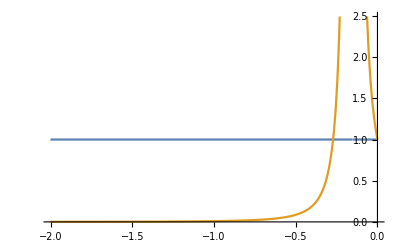

```mathematica
(*Checking if a solution exists. We equate the Claussius Clayperon equation for [100] and [001] loading as they have the same change in entropy. We test if a solution cna exist*)
f1[x_]:=1/((1+6.5*x)^2*(1-2.6*x))
f2[y_]:=Sin[y]
Plot[{1,f1[x]},{x,-2,0}]
```